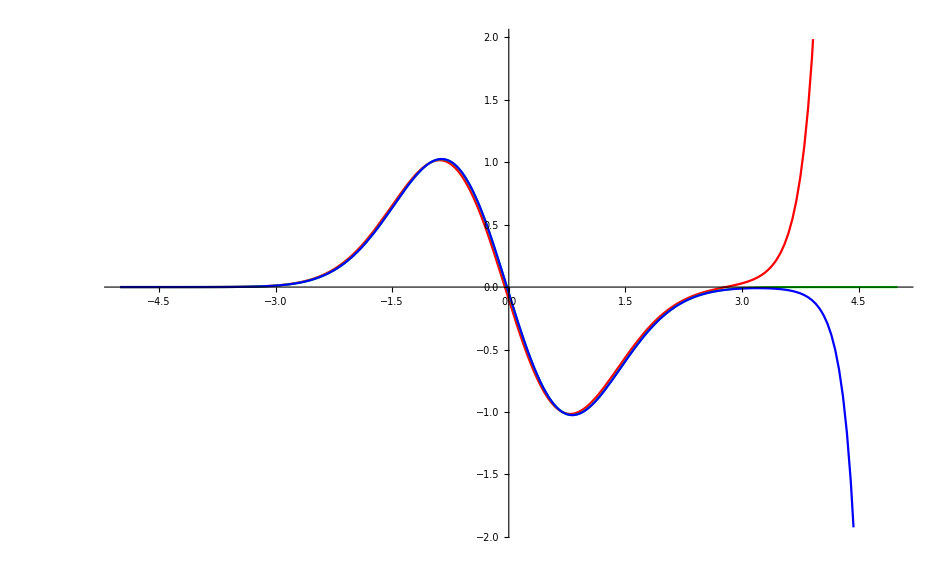

```mathematica
h=5/100 ;
m=1;
V[x_]=x^2;

(* h=5/200 , [-10, 10] e=2.121125011633008271125249263642270316752`300; *) 
e=2.121125011633008271125249263642270316752`300;

Q[x_]=2*m(e-V[x]);
κ[x_]=√(-Q[x]);

(* Three Points *)
xmin=-10;
xmax=-xmin;
nP=(xmax-xmin)/h+1;
ψ3p={{xmin,0},{xmin+h,10^-16}};
Do[
x= xmin+h(n-1);
newValue = ψ3p[[n-1,2]]*(2-h^2 Q[x])-ψ3p[[n-2,2]];
ψ3p=Join[ψ3p,{{x,newValue}}];,{n,3,nP}]
f3p=Interpolation[ψ3p,InterpolationOrder->1];
(* ------------------------------------------------- *)
ψ3pFiner={{xmin,0},{xmin+h/2,10^-16}};
nPFiner=2(xmax-xmin)/h+1;
Do[
x= xmin+h/2(n-1);
newValue = ψ3pFiner[[n-1,2]]*(2-h^2/4 Q[x])-ψ3pFiner[[n-2,2]];
ψ3pFiner=Join[ψ3pFiner,{{x,newValue}}];,{n,3,nPFiner}]
f3pFiner=Interpolation[ψ3pFiner,InterpolationOrder->1];
(* ------------------------------------------------- *)
Clear[x,n,f3pExtra]
f3pExtra[x_]=(4f3pFiner [x]-f3p[x])/3;

Plot[{f3p[x]/f3p[-1],f3pFiner[x]/f3pFiner[-1],f3pExtra[x]/f3pExtra[-1]},{x,-5,5},PlotStyle->{Red,Green,Blue},PlotRange->Automatic]
```

```mathematica
2.1211250116329888`20
```

2.1211250116329888

```mathematica
Clear[Q,y,V,e,m]
V[x_]=x^2;
D[2*m(e-V[x])y[x],{x,6}]
```

2 m (-30 y^(4)[x]-12 x y^(5)[x]+(e-x^2) y^(6)[x])